# Generating Realistic Cities with Perlin Noise

## Abstract

Abstract

## Introduction

### What is Perlin noise?

In computer graphics and game design, procedural generation offers a way to create vast and detailed worlds without having to hand-craft every element. One of the earliest and most influential tools for this is Perlin noise, an algorithm that is often used in terrain generation within video games, first published in 1985 by NYU professor Ken Perlin. 

The difference between Perlin noise and regular random noise is that while pure randomly generated noise can be chaotic and erratic, Perlin noise produces smooth, pseudo-random patterns that can be layered at different frequencies to mimic natural textures and terrain. It is useful in generating natural-looking randomness with specific desirable properties which makes it perfect for simulating natural-looking patterns, which in our case will be cities. One of the most popular examples of the use of Perlin noise is the terrain generation for the video game Minecraft.

In this project, we will be using Ken Perlin’s Improved Perlin Noise which he published in 2002.

## Creating Perlin Noise

NOTE: I would like to preface this section by mentioning that a lot of it is taken from this wonderful article by Flafla2. That article gives a C# version of the Improved Perlin Noise function. The original Improved Perlin Noise code is written in Java.

### Logical overview

Starting with the basic Perlin Noise function, for the input, we will take three coordinate parameters, {x,y,z} which will all be decimal coordinates and our output will be a decimal number between 0.0 and 1.0.

First we will divide the x, y, and z coordinates into unit cubes. 
This basically means that we will find [x,y,z]%1.0 to separate the decimal part of the coordinate in order to find the coordinate’s location within the 1x1 cube.

Visualizing this concept in 2 dimensions(only x and y):

-Graphics-

The blue dot represents an input coordinate and the four points making up the square are the surrounding integral unit coordinates.

On each of the 4 unit coordinates making up the square, we generate a pseudorandom gradient vector. The gradient vector defines a positive direction(the direction where the vector points to) and a negative direction(the direction opposite of where the vector points to). 
Pseudorandom means that the value given is deterministic and for any input given into the gradient vector equation, it will only give one kind of output. Although the output will seem random, it isn’t truly random. This also means that each integral coordinate has its “own” gradient that will never change if the gradient function doesn’t change.

Example of some gradient vectors:

While the original Perlin Noise uses completely random gradients, in Ken Perlin’s Improved Noise, we will be using gradients picked from the vectors of the point in the center of a cube to the edges of the cube:

(1,1,0),(-1,1,0),(1,-1,0),(-1,-1,0),
(1,0,1),(-1,0,1),(1,0,-1),(-1,0,-1),
(0,1,1),(0,-1,1),(0,1,-1),(0,-1,-1)

The reason why the Improved Noise version does this is explained in this article.

After we pick our gradients, we need to calculate a distance vector from the four points to the given point.

Example of distance vectors

Next we take the dot product between the gradient vector and the distance vector. This will result in our final influence values.

Formula for the dot product between the gradient vector and distance vector:

grad.x * dist.x + grad.y * dist.y + grad.z * dist.z

This function is derived from the definition of a dot product which is the product of the magnitudes of 2 vectors multiplied with the cosine of the angle between the two vectors.

```mathematica
dot[vec1_,vec2_]:=Cos[VectorAngle[vec1,vec2]]*vec1//Normalize*vec2//Normalize;
```

This will result in a positive value when the vectors are in the same direction and a negative value when the vectors are in opposite directions.
Here is an example of a visual representing the positive and negative influences

Visualization of influenced in 2D noise:

Finally, we need to interpolate between these 4 values in order to get a weighted average between the 4 grid points.
We accomplish this by getting the average of the averages.

Assuming lerp[] is our linear interpolation function, g1, g2, g3, g4  are our dot product values, and  u, v are our coordinates of the location of the input coordinate its unit square(back when we did [x,y,z]%1.0), we get our weighted average by doing something like this:

```mathematica
x1=lerp[g1,g2,u];
x2=lerp[g3,g4,u];
average=lerp[x1,x2,v];
```

Our final step addresses one problem. The weighted average received above is not the best since linear interpolation often look unnatural. We can get a smoother transition between gradients by using a fade function(also called an ease curve).

Example of a fade function(ease curve):

The Perlin Noise Function uses  as its fade function.

### Code Breakdown

#### Setup

The first thing to do is to set up a permutation table which we will call p[]. We will make an array of number 0-255 inclusive in a random order.

Creating a random permutation of the numbers 0-255. In order to avoid overflow, we will double the list.

```mathematica
permutation = RandomSample[Range[0, 255]];
p = Join[permutation, permutation];
```

To start off our perlin function, we need to decide a repeat value.

```mathematica
repeat=255;
```

In this case, our noise will repeat and show patterns every 255 units we move our coordinates. We will use the Mod function to get the remainder so that if our input overflow over the repeat value, the modulo will keep it the coordinate between (-repeat,repeat).

While I will explain more about this later, the repeat value is mainly used to make the perlin noise repeat over values smaller than 256 because the perlin noise function will always repeat at least every 256 coordinates. In this project, the repeat value will not be relevant.

Perlin will take in x, y, and z coordinates. It will start by modding the values over the repeat value.

```mathematica
perlin[a_, b_, c_] :=Module[
{x=a, y=b, z=c},

If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}]; 

(*...*)
]
```

Next we need variables(xi, yi, zi) that will represent the unit cube that our coordinate is in. To first find the unit cube, we use the Floor function on each coordinate value. Then, we bind the coordinate values to the range [0,255] using modulo(remainder) over 256 so we won’t run into a Part error due to the index being too big when we access the p[] array. 

However instead of using Mod[x,256] to achieve this, the BitAnd function has the unique property of being able to do the same thing for any powers of 2 by inputting the power of 2 we want to mod by minus 1. 
This means that the following two lines of code will do the same thing:
Mod[x,256]
BitAnd[x,255]
If you would like to understand better on how this works, learn more about binary numbers and bit string flicking/bitwise operations.

This will the have the effect of Perlin noise repeating every 256 coordinates which is unfortunate if trying to use this for large maps. However, this problem can be fixed by simply using decimal coordinates since Perlin works with decimal coordinates. For example if we want to create a noise map 1000x1000 with no repeats, we can increment each coordinate by 0.1 so that the x, y, and z values used will only range [1,100].

We will then find the location of our coordinate inside the unit cube and assign these values to variables xf, yf, zf. This is essentially,  n=n%1.0 where n is a coordinate.

```mathematica
perlin[a_, b_, c_] :=Module[
{x=a, y=b, z=c,xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255]},

(*..*)
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z];  
(*...*)
]
```

#### The Fade Function

The Perlin Noise Fade Function:


The Fade function, defined by Ken Perlin, eases coordinate values so that they will ease towards integral values. This ends up smoothing the final output.

We implement this in code as shown:

```mathematica
fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
```

The fade function will be used on the coordinates inside the unit cube which we will save for interpolation later.

```mathematica
perlin[a_, b_, c_] :=Module[
{x=a, y=b, z=c,xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255],u,v,w},

(*..*)
u = fade[xf]; v = fade[yf]; w = fade[zf];
(*...*)
]
```

#### The Hash Function

The Perlin Noise hash function is used to get a distinct value for every coordinate input.

The hash function is used outside of Perlin Noise and has other applications.

Defined by Wikipedia: “any function that can be used to map data of arbitrary size to data of fixed size, with slight differences in input data producing very big differences in output data.”

In our application of the hash function, we hash all 8 unit cube coordinates surrounding the input coordinate. 
We will create a helper function inc[] to increment the numbers and make sure the noise repeats.

```mathematica
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];
```

Note: our implementation of the hash function was increment each index/part by 1 since Wolfram lists start their index with 1.

Hash function inside the Perlin Noise Function:

```mathematica
perlin[a_, b_, c_] :=Module[
{x=a, y=b, z=c,xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255],u,v,w,aaa, aba, aab, abb, baa, bba, bab, bbb},

(*..*)
aaa =p[[p[[p[[        xi  + 1]]+         yi  +1]]+         zi   +1]];aba=p[[p[[p[[         xi  + 1]]+inc[yi]+1]]+        zi   +1]];aab=p[[p[[p[[         xi  + 1]]+         yi  +1]]+inc[zi]+1]]; abb=p[[p[[p[[         xi  + 1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+          yi  + 1]]+       zi  +1]];bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+         zi  +1]];bab=p[[p[[p[[inc[xi]+1]]+         yi  +1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
(*...*)
]
```

This hash function gives a value between 0 and 255(inclusive) from our p[] array.

#### The Gradient Function

The goal of the gradient function is to calculate the dot product of a randomly selected gradient vector and the 8 location vectors.
To achieve this, we will pick a random vector from the 12 vectors given:

```mathematica
(1,1,0),(-1,1,0),(1,-1,0),(-1,-1,0),
(1,0,1),(-1,0,1),(1,0,-1),(-1,0,-1),
(0,1,1),(0,-1,1),(0,1,-1),(0,-1,-1)
```

This is determined by the last 4 bits of the hash function value (the first parameter of grad[]). The other 3 parameters represent the location vector (that will be used for the dot product).

Picks a random vector based on hash and returns the dot product:

```mathematica
grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
```

The original Perlin Noise code uses bit-flipping code to accomplish this.

#### Combining all the parts

We can now use all functions we defined above and use them for the 8 surrounding unit cube coordinates and interpolate them together

Linear Interpolate:

```mathematica
lerp[a_,b_,x_] :=a+x*(b-a);
```

We will use the variables x1, x2, y1, y2 in order to store the dot product between a pseudorandom gradient vector and the vector from the input coordinate to the 8 surrounding points in the unit cube.
We will then take the linear interpolation of all the values to get a weighted average based on the faded values we defined before(u, v, w).

Calculating the final noise value by getting the linear interpolation:

```mathematica
perlin[a_, b_, c_] :=Module[
{x=a, y=b, z=c,xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255],u,v,w,aaa, aba, aab, abb, baa, bba, bab, bbb,x1,x2,y1,y2},

(*..*)
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
(lerp[y1, y2, w]+1)/2
];
```

Putting it all together:

### Final Perlin Noise function code

#### initial values and helper functions

```mathematica
permutation = RandomSample[Range[1, 256]];
p = Join[permutation, permutation]; 
repeat = 255;
fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];
grad[hash_, x_, y_, z_] := Module[{hashy = BitAnd[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);
```

#### Perlin Noise Function

```mathematica
perlin[a_, b_, c_] := Module[{xi = BitAnd[Floor[a], 255], yi = BitAnd[Floor[b], 255], zi = BitAnd[Floor[c], 255], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa =p[[p[[p[[        xi   +1]]+yi+1]]+        zi    +1]]; aba = p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]]; aab=p[[p[[p[[         xi   +1]]+yi+1]]+inc[zi]+1]]; abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+          zi  +1]]; bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]]; bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
(lerp[y1, y2, w]+1)/2];
```

#### Perlin Noise with Octaves

```mathematica
octavePerlin[x_,y_,z_,octaves_,persistence_]:=Module[{total=0, frequency=1,amplitude=1,maxValue=0},
total = perlin[x*frequency,y*frequency,z*frequency]*amplitude + Total[Table[maxValue+= amplitude;amplitude*=persistence;frequency*=2;perlin[x*frequency,y*frequency,z*frequency]*amplitude, {i,octaves-1}]]; total/maxValue];
```

### 3D visual

```mathematica
Plot3D[octavePerlin[x,y,250,6,0.8],{x,20,21},{y,10,11}]
```

-Graphics3D-

```mathematica
Plot3D[RandomReal[],{i,0,1},{j,0,1}]
```

This is random noise:

-Graphics3D-

It is very ugly :(.

```mathematica
Plot3D[octavePerlin[x,y,0.06,6,0.6],{x,22,21},{y,10,11}]
```

This is perlin noise:

-Graphics3D-

Much better :D.

## Street structure generation

### Algorithm

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False, sizeFactor},
    
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];

  stack={{0,0,worldWidth,worldHeight}};

  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
(*sizeFactor=Echo[smoothstep[1,2,Min[R[[3]]/minBlock,R[[4]]/minBlock]]];*)
(*sizeFactor=1;*)
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

### World settings

```mathematica
worldWidth=250;
worldHeight=250;
minBlock=15;
maxJitter=5;
roadWidth=5;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;
mapGrid=Table[0,{x,worldWidth},{y,worldHeight}];
```

### Road Skeleton Generation

```mathematica
mapGrid=Table[0,{x,worldWidth},{y,worldHeight}];
roadsCoords=generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff]
```

{{1,128.742,250,128.742,5},{129.273,1,129.273,128.742,5},{129.609,128.742,129.609,250.,5},{60.1686,1,60.1686,128.742,5},{129.273,59.4043,250.,59.4043,5},{69.0412,128.742,69.0412,250.,5},{129.609,191.527,250.,191.527,5},{60.1686,59.9401,129.273,59.9401,5},{191.83,1,191.83,59.4043,5},{190.29,59.4043,190.29,128.742,5},{1,184.984,69.0412,184.984,5},{69.0412,186.08,129.609,186.08,5},{187.68,128.742,187.68,191.527,5},{191.934,191.527,191.934,250.,5},{98.8692,1,98.8692,59.9401,5},{97.4339,59.9401,97.4339,128.742,5},{158.506,1,158.506,59.4043,5},{191.83,33.0304,250.,33.0304,5},{129.273,89.2397,190.29,89.2397,5},{190.29,91.2373,250.,91.2373,5},{38.535,128.742,38.535,184.984,5},{95.0573,128.742,95.0573,186.08,5},{69.0412,219.755,129.609,219.755,5},{129.609,159.386,187.68,159.386,5},{187.68,157.834,250.,157.834,5},{157.329,191.527,157.329,250.,5},{191.934,216.202,250.,216.202,5},{60.1686,32.309,98.8692,32.309,5},{98.8692,28.1786,129.273,28.1786,5},{60.1686,93.2373,97.4339,93.2373,5},{97.4339,96.7122,129.273,96.7122,5},{158.506,31.6051,191.83,31.6051,5},{222.516,1,222.516,33.0304,5},{157.508,89.2397,157.508,128.742,5},{224.873,59.4043,224.873,91.2373,5},{219.34,91.2373,219.34,128.742,5},{1,152.472,38.535,152.472,5},{38.535,158.132,69.0412,158.132,5},{95.0573,156.575,129.609,156.575,5},{98.2636,186.08,98.2636,219.755,5},{98.2433,219.755,98.2433,250.,5},{153.979,128.742,153.979,159.386,5},{159.191,159.386,159.191,191.527,5},{221.255,157.834,221.255,191.527,5},{157.329,223.854,191.934,223.854,5},{217.716,216.202,217.716,250.,5},{81.9329,1,81.9329,32.309,5},{98.8692,44.9401,129.273,44.9401,5},{80.7724,59.9401,80.7724,93.2373,5},{82.4339,93.2373,82.4339,128.742,5},{97.4339,80.3162,129.273,80.3162,5},{97.4339,113.742,129.273,113.742,5},{157.508,111.908,190.29,111.908,5},{206.824,59.4043,206.824,91.2373,5},{219.34,113.742,250.,113.742,5},{15.5001,152.472,15.5001,184.984,5},{98.2636,201.08,129.609,201.08,5},{113.243,219.755,113.243,250.,5},{172.68,128.742,172.68,159.386,5},{187.68,173.49,221.255,173.49,5},{172.965,191.527,172.965,223.854,5},{217.716,235.,250.,235.,5}}

```mathematica
roadPutter[coords_]:=Module[{x1=coords[[1]]//Floor,x2=coords[[3]]//Floor,y1=coords[[2]]//Floor,y2=coords[[4]]//Floor,width=coords[[5]]},If[x1==x2,mapGrid=ReplacePart[mapGrid,{i_,j_}/;x1<=i<=x1+width&&y1<=j<=y2->1],mapGrid=ReplacePart[mapGrid,{i_,j_}/;x1<=i<=x2&&y1<=j<=y1+width->1]]];
roadPutter/@roadsCoords;
(*mapGrid//Grid;*)
```

## Identifying and Classifying Blocks with Perlin noise

### Initializing noise map

https://chatgpt.com/share/686d2448-d29c-800c-82d0-cb224cc06fd4
talk about this for the noise part

```mathematica
xcoef[]:=RandomInteger[{1,245}];
ycoef[]:=RandomInteger[{1,245}];
offset={0.37,0.57};
```

```mathematica
elevoctaves=6;elevx=xcoef[];elevy=ycoef[];zelev=RandomReal[{0,255}];elevpers=RandomReal[{0.3,0.6}];
elevnoiseMap=ParallelTable[octavePerlin[x,y,zelev,elevoctaves,elevpers],{x,elevx,elevx+10,10/worldWidth},{y,elevy,elevy+10,10/worldHeight}];

poploctaves=6;poplx=xcoef[];poply=ycoef[];zpopl=RandomReal[{0,255}];poplpers=RandomReal[{0.3,0.6}];
poplnoiseMap=ParallelTable[octavePerlin[x,y,zpopl,poploctaves,poplpers],{x,poplx,poplx+10,10/worldWidth},{y,poply,poply+10,10/worldHeight}];

poproctaves=6;poprx=xcoef[];popry=ycoef[];zpopr=RandomReal[{0,255}];poprpers=RandomReal[{0.3,0.6}];
poprnoiseMap=ParallelTable[octavePerlin[x,y,zpopr,poproctaves,poprpers],{x,poprx,poprx+10,10/worldWidth},{y,popry,popry+10,10/worldHeight}];
```

```mathematica
ListPlot3D[elevnoiseMap]
```

-Graphics3D-

### Finding the blocks

```mathematica
visited=mapGrid;
zeroBlocks={};
findDownRight[x_,y_,grid_]:=Module[{i=x,j=y},If[visited[[x,y]]==0,Until[i>worldWidth,If[grid[[i,j]]!=1,i++,Break[]]];i--;
Until[j>worldHeight,If[grid[[i,j]]!=1,j++,Break[]]];j--;
visited=ReplacePart[visited,{a_,b_}/;x<=a<=i&&y<=b<=j->1];
AppendTo[zeroBlocks,{x,y,i,j}]]];

Table[findDownRight[x,y,mapGrid],{x,worldWidth},{y,worldHeight}];
zeroBlocks
```

{{1,1,59,127},{1,134,37,151},{1,158,14,183},{1,190,68,250},{21,158,37,183},{44,134,68,157},{44,164,68,183},{66,1,80,31},{66,38,97,58},{66,65,79,92},{66,99,81,127},{75,134,94,185},{75,192,97,218},{75,225,97,250},{86,65,96,92},{87,1,97,31},{88,99,96,127},{101,134,128,155},{101,162,128,185},{103,65,128,79},{103,86,128,95},{103,102,128,112},{103,119,128,127},{104,1,128,27},{104,34,128,43},{104,50,128,58},{104,192,128,200},{104,207,128,218},{104,225,112,250},{119,225,128,250},{135,1,157,58},{135,65,189,88},{135,95,156,127},{135,134,152,158},{135,165,158,190},{135,197,156,250},{159,134,171,158},{163,95,189,110},{163,117,189,127},{163,197,171,222},{163,229,190,250},{164,1,190,30},{164,37,190,58},{165,165,186,190},{178,134,186,158},{178,197,190,222},{193,134,250,156},{193,163,220,172},{193,179,220,190},{196,65,205,90},{196,97,218,127},{197,1,221,32},{197,39,250,58},{197,197,250,215},{197,222,216,250},{212,65,223,90},{223,222,250,234},{223,241,250,250},{225,97,250,112},{225,119,250,127},{227,163,250,190},{228,1,250,32},{230,65,250,90}}

### Classify the blocks

#### Classify by high noise and low noise

```mathematica
(*land[n_]:=Which[n<.45,"park",n<.60,"lowrise",True,"highrise"];*)highnoise=0.525;midnoise=0.485;lownoise=0.45;
land[n_,pr_,pl_]:=Which[pr>=highnoise&&n<=highnoise&&pl<=lownoise,"park",n>=highnoise&&pl>=midnoise,"business",pr<=midnoise&&n<=highnoise,"industrial",pr>=highnoise&&pl>=highnoise&&n<=highnoise,"commercial",True,"residential"];
tileColors=<|"road"->Black,"background"->White,"park"->Green,"residential"->Red,"industrial"->Darker[Green],"commercial"->Darker[Blue],"business"->Darker[Cyan]|>;
tileToNumber=AssociationThread[Keys[tileColors],{1,0,3,4,5,6,7}];
numberToTile=AssociationThread[{1,0,3,4,5,6,7},Keys[tileColors]];
(*offset={0.37,0.57};
xcoef=0.05;ycoef=0.05;z[]:=RandomReal[{0,255}];*)
blockOctaves=6;blockPersistence=0.55;
```

```mathematica
getBlockMid[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},{Floor[Mean[{x1,x2}]],Floor[Mean[{y1,y2}]]}];(*classifyBlock[coords_]:=Module[{x=getBlockMid[coords][[1]],y=getBlockMid[coords][[2]]},land[octavePerlin[x*xcoef,y*ycoef,z[],blockOctaves,blockPersistence]]];*)
classifyBlock[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],elevnoise,poprnoise,poplnoise},elevnoise=Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]];
poprnoise=Mean[Flatten[poprnoiseMap[[x1;;x2,y1;;y2]]]];
poplnoise=Mean[Flatten[poplnoiseMap[[x1;;x2,y1;;y2]]]];
land[elevnoise,poprnoise,poplnoise]]
applyBlockType[coords_]:=Module[{l=classifyBlock[coords],x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},mapGrid=ReplacePart[mapGrid,{a_,b_}/;x1<=a<=x2&&y1<=b<=y2->tileToNumber[l]]]
```

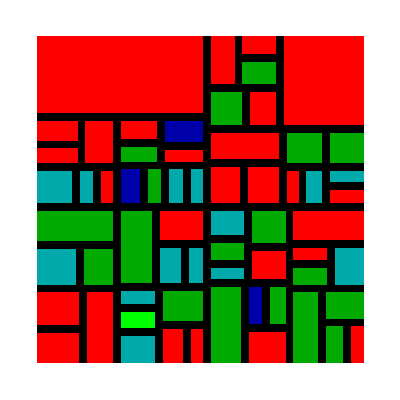

```mathematica
applyBlockType[#]&/@zeroBlocks;
ArrayPlot[mapGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False]
```

### Give each block a height based on elevation noise

```mathematica
getElevationNoise[coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]]},Mean[Flatten[elevnoiseMap[[x1;;x2,y1;;y2]]]]]

Module[{blockType,initHeight},Table[blockType=mapGrid[[zeroBlocks[[x]][[1]]]][[zeroBlocks[[x]][[2]]]];
initHeight=Floor[Rescale[getElevationNoise[zeroBlocks[[x]]],{0.30,0.7},{1,10}]];
AppendTo[zeroBlocks[[x]],Which[blockType==tileToNumber["park"],1,blockType==tileToNumber["business"],Min[{Floor[2*initHeight],10}],blockType==tileToNumber["industrial"],Max[2,Floor[0.6*initHeight]],True,initHeight]],{x,zeroBlocks//Length}]];
```

```mathematica
blockHeightGiver[grid_,coords_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],h=coords//Last},ReplacePart[grid,{y_,a_,b_}/;(y>h&&x1<=a<=x2&&y1<=b<=y2)||(y>1&&grid[[y]][[a]][[b]]==1)->tileToNumber["background"]]]
```

### 3D visualization

```mathematica
numLevels=10;
mapGrid3D=Table[mapGrid,{x,numLevels}];
Table[mapGrid3D=blockHeightGiver[mapGrid3D,zeroBlocks[[i]]],{i,zeroBlocks//Length}];
```

```mathematica
ArrayPlot3D[mapGrid3D,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],BoxRatios->{1,1,1}]
```

-Graphics3D-

## Spawn Entities on City Blocks

```mathematica
(*tileColors=<|"road"->Black,"background"->White,"park"->Green,"residential"->Red,"industrial"->Darker[Green],"commercial"->Darker[Blue],"business"->Darker[Cyan]|>;
tileToNumber=AssociationThread[Keys[tileColors],{1,0,3,4,5,6,7}];*)colors={White,Black,Gray,Green,Red,Darker[Green],Darker[Blue],Darker[Cyan],Cyan,Blue,Darker[Brown],Brown,Darker[Gray]};
colorData=Thread[Range[0,(colors//Length)-1]->colors];
emptymapGrid=Table[0,{x,mapGrid//Length},{y,mapGrid[[1]]//Length}];
city3D=Prepend[Table[emptymapGrid,49],mapGrid];
```

```mathematica
colorData
```

{0→GrayLevel[1],1→GrayLevel[0],2→GrayLevel[0.5],3→RGBColor[0, 1, 0],4→RGBColor[1, 0, 0],5→RGBColor[0, Rational[2, 3], 0],6→RGBColor[0, 0, Rational[2, 3]],7→RGBColor[0, Rational[2, 3], Rational[2, 3]],8→RGBColor[0, 1, 1],9→RGBColor[0, 0, 1],10→RGBColor[0.4, 0.2666666666666667, 0.13333333333333336],11→RGBColor[0.6, 0.4, 0.2],12→RGBColor[0.33333333333333337, 0.33333333333333337, 0.33333333333333337]}

```mathematica
Thread[Values[tileToNumber]->Values[tileColors]]
```

{1→GrayLevel[0],0→GrayLevel[1],3→RGBColor[0, 1, 0],4→RGBColor[1, 0, 0],5→RGBColor[0, Rational[2, 3], 0],6→RGBColor[0, 0, Rational[2, 3]],7→RGBColor[0, Rational[2, 3], Rational[2, 3]]}

#### entity defs

```mathematica
tree={
{{0,0,0},
{0,10,0},
{0,0,0}},
{{0,0,0},
{0,10,0},
{0,0,0}},
{{0,5,0},
{5,5,5},
{0,5,0}},
{{0,0,0},
{0,5,0},
{0,0,0}}};
house={
{{11,11,11},
{11,11,11},
{11,10,11}},
{{11,11,11},
{11,11,11},
{11,10,11}},
(*{{11,11,11},
{11,11,11},
{11,11,11}},*)
{{10,10,10},
{10,10,10},
{10,10,10}},
{{0,10,0},
{0,10,0},
{0,10,0}}};
apartment={
{{2,2,2},
{2,2,2},
{2,2,2},
{2,2,2}},
{{8,2,8},
{2,2,2},
{2,2,2},
{8,2,8}},
{{2,2,2},
{2,2,8},
{8,2,2},
{2,2,2}},
{{8,2,8},
{2,2,2},
{2,2,2},
{8,2,8}},
{{2,2,2},
{8,2,2},
{2,2,8},
{2,2,2}},
{{8,2,8},
{2,2,2},
{2,2,2},
{8,2,8}},
{{2,2,2},
{2,2,2},
{2,2,2},
{2,2,2}}};
factory={
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}},
{{12,9,12,9,12},
{9,12,12,12,9},
{12,12,12,12,12},
{9,12,12,12,9},
{12,9,12,9,12}},
{{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12},
{12,12,12,12,12}}};
{{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},(*level 1 part 1*)
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},(*level 1 part 1*)
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,8,8,12,8,8,12,8,8,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,12,12,12,12,12,12,12,12,12},
{8,12,12,12,12,12,12,12,12,8},
{8,12,12,12,12,12,12,12,12,8},
{12,8,8,12,8,8,12,8,8,12}},
{{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12},
{12,12,12,12,12,12,12,12,12,12}}, (*level 1 part 2*)
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},(*level 2 ends*)
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,8,12,12,12,12,8,0,0},
{0,0,12,8,8,12,8,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,12,12,12,12,12,12,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},(*level 2 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,8,12,12,8,0,0,0},
{0,0,0,12,8,8,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,12,12,12,12,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},(*level 3 starts*)
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}},
{{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,12,12,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}}}//Iconize
```

```mathematica
skyscraper=;
```

### visual

```mathematica
Length@skyscraper
```

30

```mathematica
ArrayPlot3D[skyscraper,ColorRules->colorData]
```

-Graphics3D-

```mathematica
(*city3D[[2;;5,1;;3,1;;3]]=tree;
city3D[[2;;5]][[4;;6]][[1;;3]]=house;
city3D[[2;;8]][[10;;13]][[1;;3]]=apartment;
city3D[[2;;10]][[20;;24]][[1;;5]]=factory;*)
city3D[[2;;31]][[30;;39]][[1;;10]]=skyscraper;
```

```mathematica
ArrayPlot3D[city3D,ColorRules->colorData,BoxRatios->{1, 1,0.25}]
```

-Graphics3D-

```mathematica
skyscraper//Length
```

30

### populating blocks with entities(buildings and trees)

```mathematica
parkEntities={tree};
residentialEntities={apartment,house};
businessEntities={skyscraper};
industrialEntities={factory};
commercialEntities={tree};
blockEntities={parkEntities,residentialEntities,industrialEntities,commercialEntities,businessEntities};
numToEntity=AssociationThread[{3,4,5,6,7},blockEntities];
```

func blockputter[type, coords,entity,biggestSize]:
position = jitter start
pick starting area jitter
	check size continue if too big
	PUT IT
	jitter x and da y

```mathematica
putEntity[coords_,entity_]:=Module[{x1=coords[[1]],y1=coords[[2]]},city3D[[2;;2+(entity//Length)-1,x1;;x1+(entity[[1]]//Length)-1,y1;;y1+(entity[[1,1]]//Length)-1]]=entity;];

spawnEntities[coords_,entity_]:=Module[{x1=coords[[1]],y1=coords[[2]],x2=coords[[3]],y2=coords[[4]],z=3,bigBlockZero=Table[0,{(entity[[1]]//Length)},{(entity[[1,1]]//Length)}]},
Table[
If[
bigBlockZero==city3D[[z]][[i;;i+(entity[[1]]//Length)-1,j;;j+(entity[[1,1]]//Length)-1]]&&RandomReal[]<=0.22,
putEntity[{i,j},entity],0],
{i,x1,x2-(entity//Length),RandomInteger[{2,3}]},{j,y1,y2-(entity[[1]]//Length),RandomInteger[{entity[[1]][[1]]//Length,(entity[[1]][[1]]//Length)+1}]}];]
```

(* DO THE PUTTING ENTITIES THING FOR EACH BLOCK;*)
go to each block
check block type
need to give entity based on block type(but for residentaila
	given a list of entities(per block type)
	randomly select one(?)
	call da fackin function

```mathematica
Table[spawnEntities[zeroBlocks[[i]],RandomChoice[numToEntity[mapGrid[[zeroBlocks[[i,1]],zeroBlocks[[i,2]]]]]]],{i,zeroBlocks//Length}];
```

```mathematica
spawnEntities[{153,35,161,59},tree]
```

## Final Results

## Conclusion

## Future work

## Works Cited

Flafla2. (2014, August 9). Understanding Perlin Noise. adrian’s soapbox. https://adrianb.io/2014/08/09/perlinnoise.html

Spottedleaf. (n.d.). OldGenerator (Version master) [Computer software]. GitHub. Retrieved July 3, 2025, from https://github.com/Spottedleaf/OldGenerator/

The Worldsmith Project. (2024, June 22). An algorithm for city map generation. https://zero.re/worldsmith/roadnet/

The Worldsmith Project. (2024, August 21). Block assignment: Using adjacency tables. https://zero.re/worldsmith/blockassign/

Noise generator. (n.d.). In Minecraft Wiki. Fandom. Retrieved July 5, 2025, from https://minecraft.fandom.com/wiki/Noise_generator

Perlin, K. (n.d.). Perlin noise. NYU Media Research Laboratory. Retrieved July 3, 2025, from https://mrl.cs.nyu.edu/~perlin/noise/

Perlin, K. (2002). Improving noise. ACM Transactions on Graphics, 21(3), 681–682. https://doi.org/10.1145/566654.566636